Mixed Chinese Postman Problem MCPP implementation in Mathematica
by Peter Burbery

The Mixed Chinese Postman Problem is finding the minimum cost traversal of a mixed graph that covers each edge at least once. The problem is NP hard which was proved in 1976. My goal is to program a function that computes the MCPP optimum tour for a mixed graph in Mathematica.
I constructed a mixed graph paclet and submitted, updated, and documented the functions to the Paclet Repository.

## Mixed Graph Paclet

Load the package and context:

```mathematica
PacletInstall["PeterBurbery/MixedGraphs"]
```

PacletObject[…]

```mathematica
Needs["PeterBurbery`MixedGraphs`"]
```

A mixed graph has undirected and directed arcs . A mixed graph is the graph sum of an undirected graph and a digraph. A digraph is a contraction of the phrase directed graph. An edge is symmetric and can be traversed in both directions because it is undirected. An arc is directed and can be traversed in only one direction.
A graph, short for undirected graph most of the time, has undirected edges. A digraph, short for directed graph, has directed arcs.

The function RandomMixedGraph constructs a graph with a certain number of nodes and edges and a value between 0 and 1 that determines what portion of the graph’s edges are directed arcs. 0 makes an undirected graph, 1 makes a digraph, and 0.68 makes a mix of an undirected graph and a digraph that is 0.68 directed, for example.

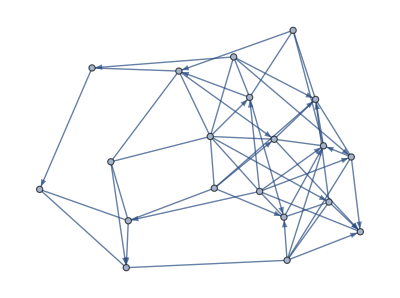

```mathematica
RandomMixedGraph[{20,54},0.68]
```

I can also construct lists of random mixed graphs:

Construct a list of 7 random mixed graphs:

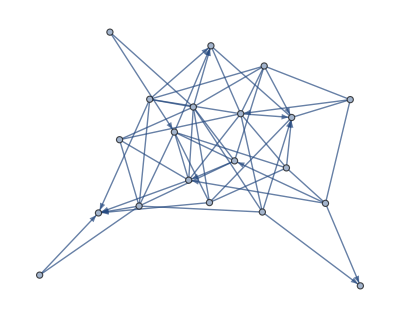
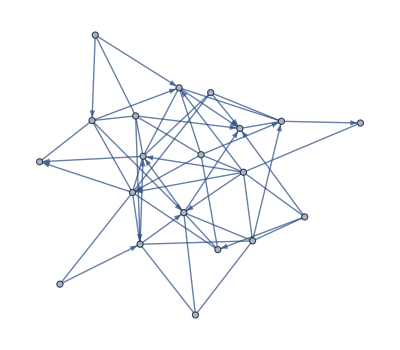
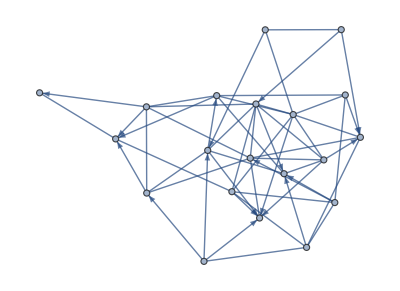
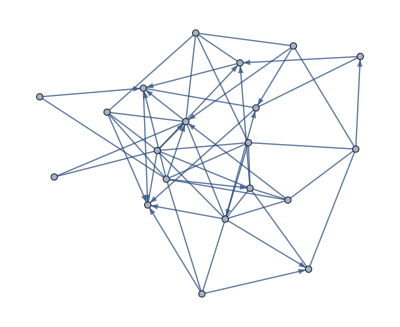
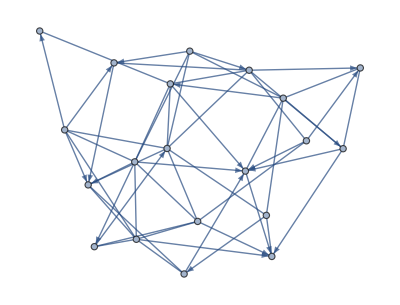
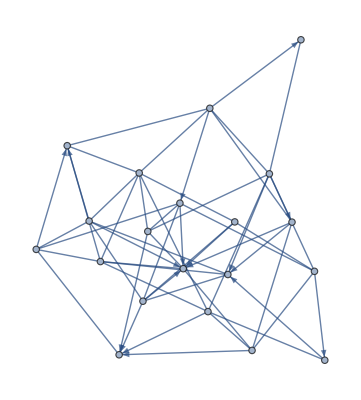
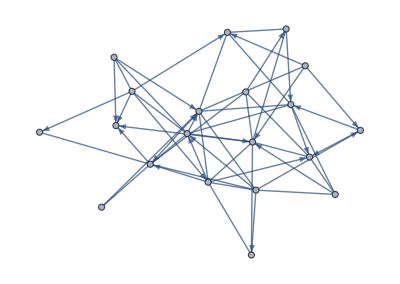

```mathematica
RandomMixedGraph[{20,54},0.68,7]
```

I can also construct an array of graphs with specific dimensions:

Create an array of random mixed graphs with dimensions {2,3,5}

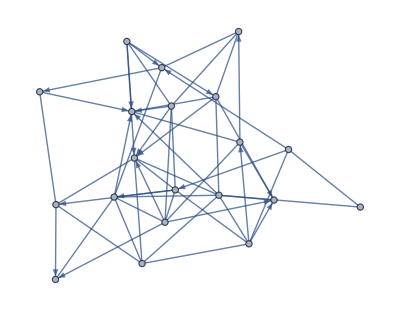
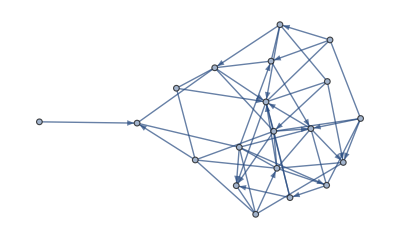
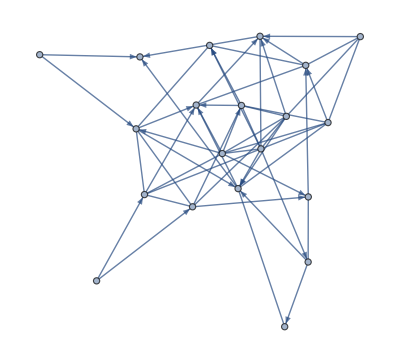
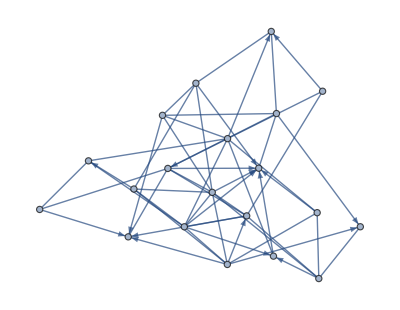
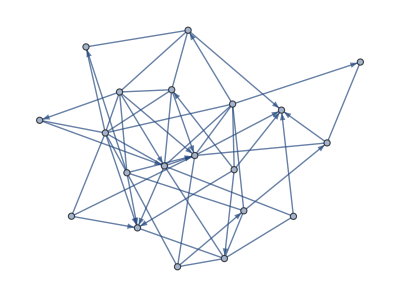
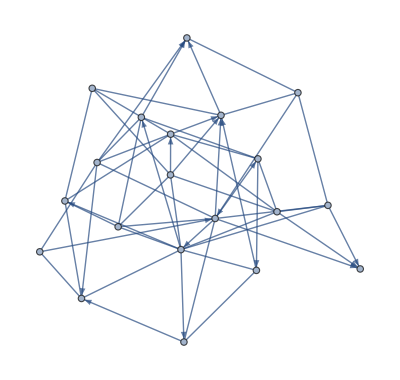
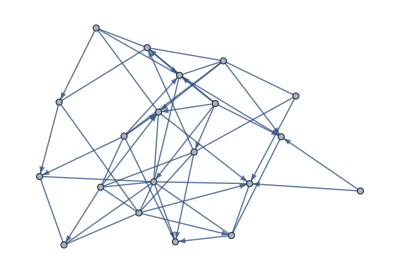
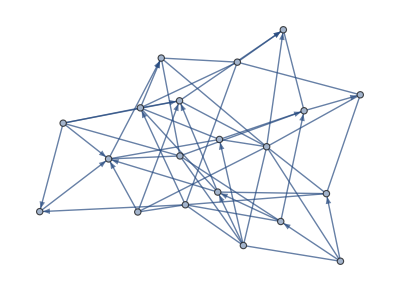

```mathematica
RandomMixedGraph[{20,54},0.68,{2,3,5},ImageSize->Tiny]
```

I created a function that converts a mixed graph into a digraph by replacing edges with pairs of arcs going in opposite directions:

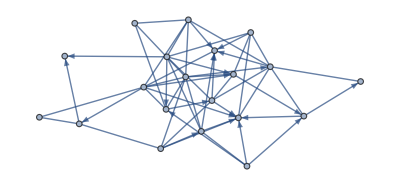

```mathematica
𝒢=RandomMixedGraph[{20,54},0.68]
```

Convert the mixed graph to a digraph:

```mathematica
MixedGraphToDigraph[𝒢]
```

-Graphics-

I also turn an undirected graph into a digraph with UndirectedGraphToMixedGraph by randomly replacing part of the edge set with directed arcs.

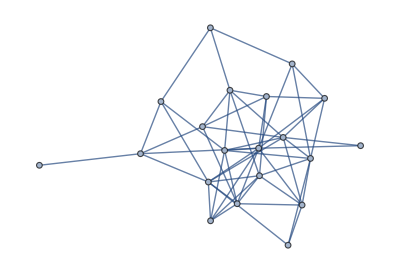

```mathematica
𝒢=RandomGraph[{20,54}]
```

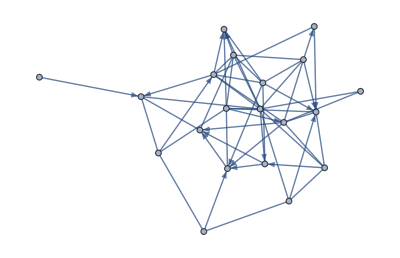

```mathematica
UndirectedGraphToMixedGraph[𝒢,0.68]
```

I can also use graph distributions instead of nodes and edges in the graph specifications argument.

Construct a random mixed graph that follows the Barabasi-Albert graph distribution:

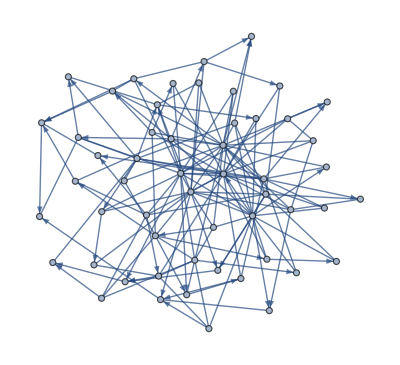

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68]
```

Construct a list of seven random mixed graphs that follows the Barabasi-Albert graph distribution:

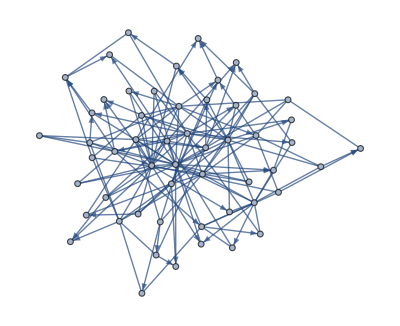
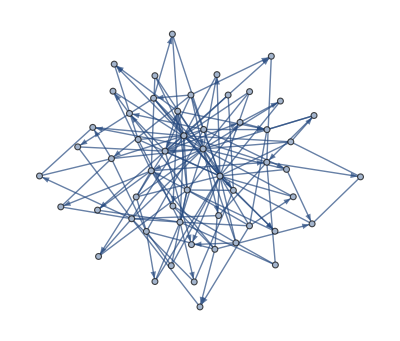
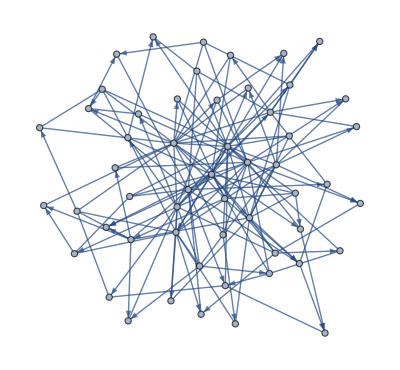
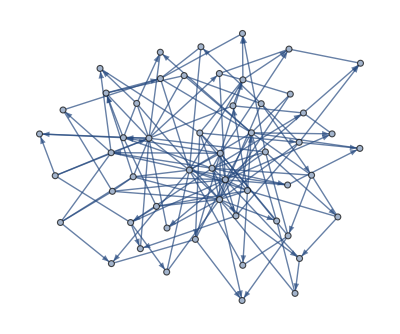
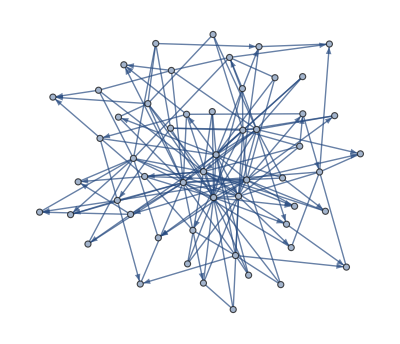
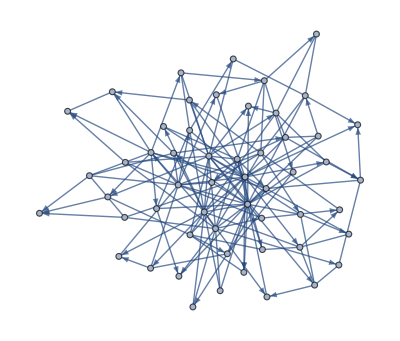
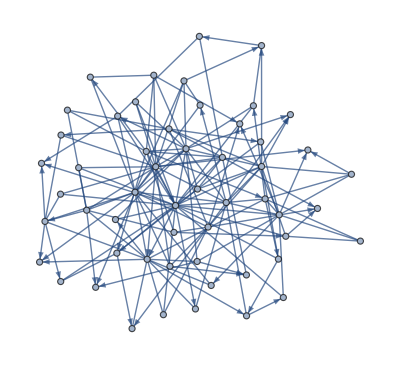

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,7]
```

Construct an 2 by 3 by 5 array of random mixed graphs that are modeled by the Barabasi-Albert graph distribution

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,{2,3,5},ImageSize->50]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

I can also use options for the random mixed graph:

Construct a large mixed graph with the large graph plot theme based on the Barabasi-Albert graph distribution:

```mathematica
RandomMixedGraph[BarabasiAlbertGraphDistribution[1000,3],0.68,PlotTheme->"LargeGraph"]
```

-Graphics-

I can also created random mixed graphs with random weights:

Construct a random mixed graphs with random real  weights

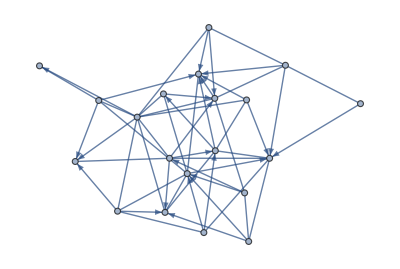

```mathematica
RandomWeightedMixedGraph[{20,54},0.68,RandomReal[]&]
```

Construct a random mixed graph with random weights that are integers in between 1 and 7:

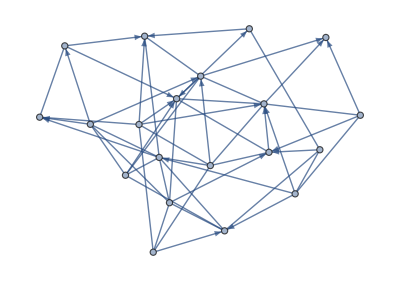

```mathematica
RandomWeightedMixedGraph[{20,54},0.68,RandomInteger[{1,7}]&]
```

I can also generate lists and arrays of random weighted mixed graphs:

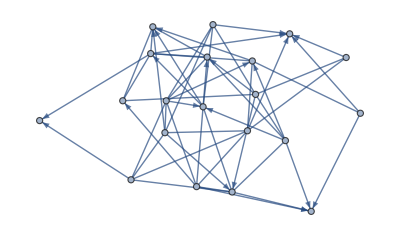
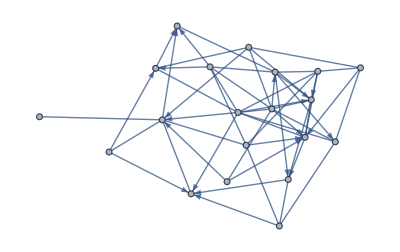
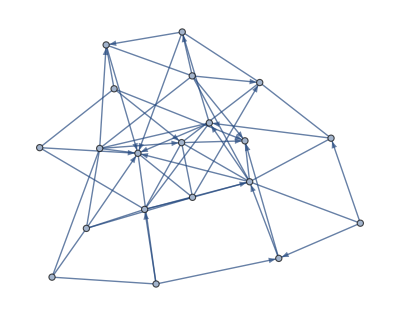
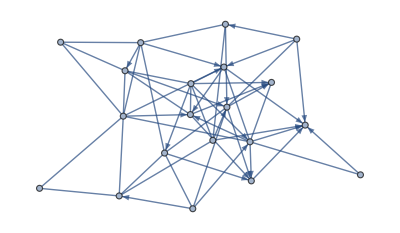
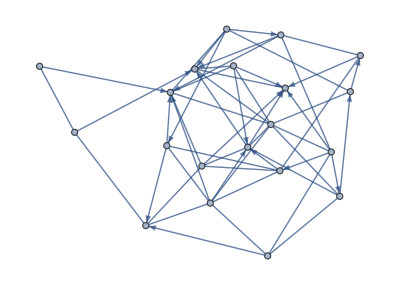
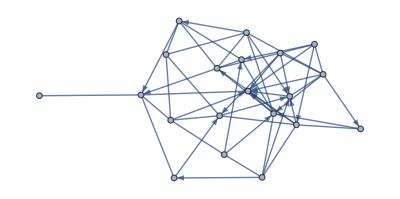
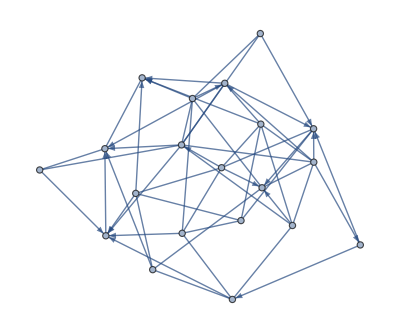

```mathematica
RandomWeightedMixedGraph[{20,54},0.68,RandomInteger[{1,7}]&,7]
```

```mathematica
RandomWeightedMixedGraph[{20,54},0.68,RandomInteger[{1,7}]&,{2,3,5},ImageSize->70]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

I can select the undirected edge set and the directed arc set of a mixed graph with MixedGraphUndirectedEdges and MixedGraphDirectedArcs, respectively:

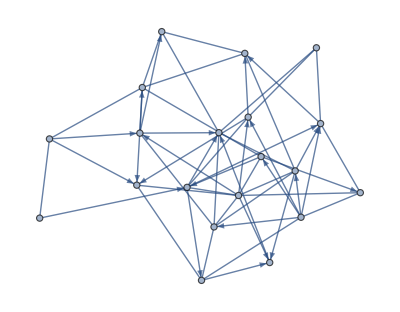

```mathematica
𝒢=RandomWeightedMixedGraph[{20,54},0.68,RandomInteger[{1,7}]&]
```

```mathematica
MixedGraphUndirectedEdges[𝒢]
```

{1<->14,2<->12,2<->15,3<->8,3<->20,5<->17,5<->19,6<->13,7<->14,10<->12,10<->17,11<->13,11<->15,12<->20,13<->17,14<->19,17<->18,18<->19}

```mathematica
MixedGraphDirectedArcs[𝒢]
```

{1->9,1->20,1->4,2->5,2->6,2->7,2->10,2->11,3->6,3->9,3->16,3->7,3->10,3->5,3->15,4->8,5->11,5->10,5->16,6->19,6->20,6->8,7->8,7->15,8->11,8->12,8->17,9->14,9->17,9->18,9->10,11->19,12->16,14->20,14->18,16->17}

I can also use a graph distribution:

Construct random mixed graphs with a graph distribution:

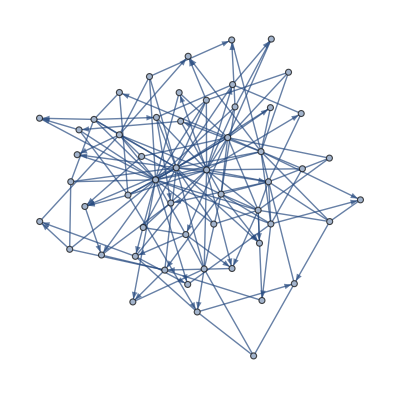

```mathematica
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,RandomInteger[{1,7}]&]
```

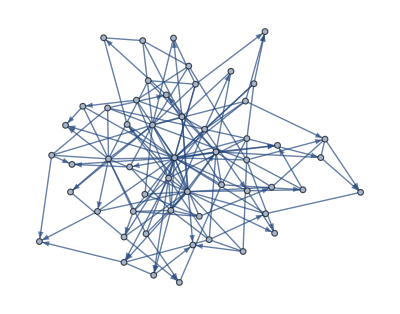
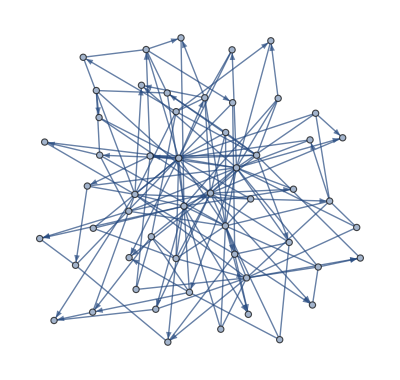
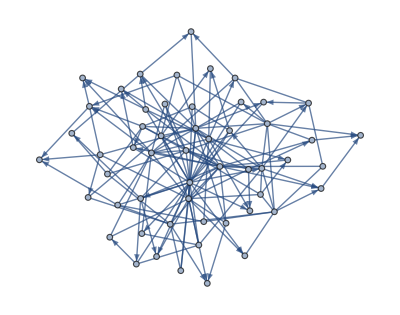
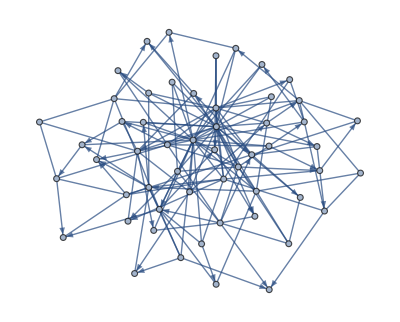
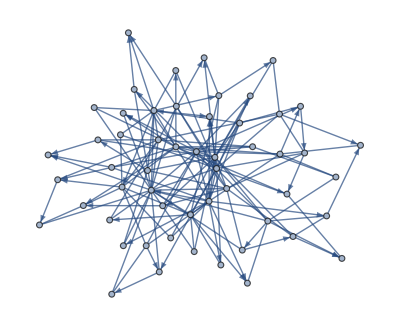
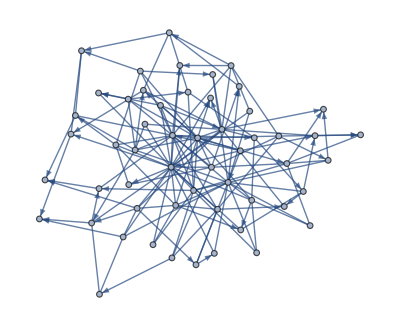
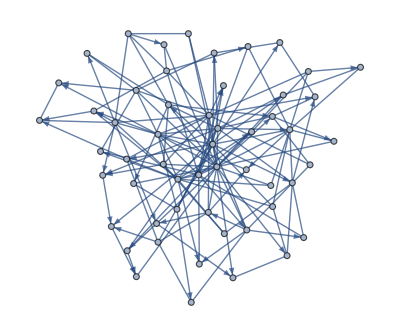

```mathematica
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,RandomInteger[{1,7}]&,7]
```

```mathematica
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,RandomInteger[{1,7}]&,{2,3,5},ImageSize->54]
```

{{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}},{{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}}}

I can also specify options for the random weighted mixed graph:

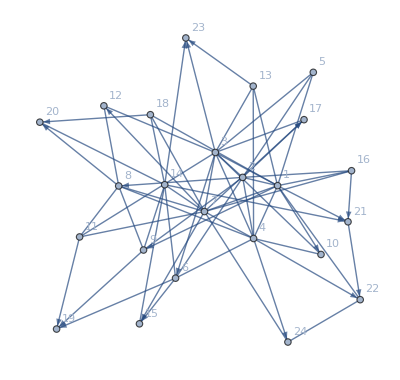

```mathematica
RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[24,3],0.68,RandomInteger[{1,7}],VertexLabels->Automatic]
```

## Graph Properties and Data

I built a function GraphInformation that computes boolean properties for graphs:

Compute graph properties for the Petersen graph:

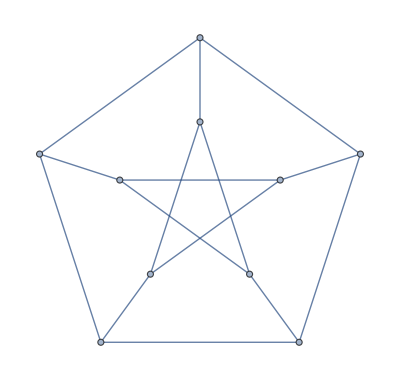

```mathematica
PetersenGraph[]
```

```mathematica
GraphInformation[PetersenGraph[]]
```

<|Acyclic→False,Bipartite→False,Complete→False,Connected→True,EdgeTransitive→True,WeightedEdge→False,Empty→False,Eulerian→False,Hamiltonian→False,LoopFree→True,Mixed→False,Path→False,Planar→False,Simple→True,Tree→False,Undirected→True,VertexTransitive→True,WeightedVertex→False,WeaklyConnected→True,Weighted→False|>

The function cannot evaluate if a mixed graph is Eulerian because the function EulerianGraphQ does not support mixed graphs. This is a topic of further research that I am working on.

EulerianGraphQ::ngen: The generalized EulerianGraphQ[Graph[<54>, <156>]] is not implemented.

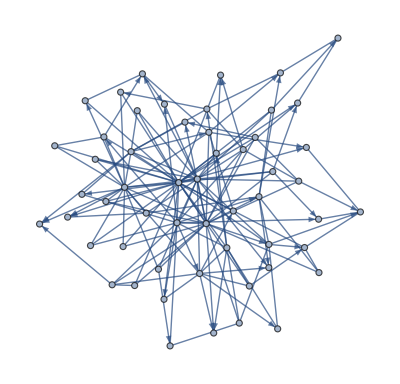
<|Acyclic→False,Bipartite→False,Complete→False,Connected→False,EdgeTransitive→False,WeightedEdge→True,Empty→False,Eulerian→EulerianGraphQ[-Graphics-],Hamiltonian→False,LoopFree→True,Mixed→True,Path→False,Planar→False,Simple→True,Tree→False,Undirected→False,VertexTransitive→False,WeightedVertex→False,WeaklyConnected→True,Weighted→True|>

```mathematica
GraphInformation[RandomWeightedMixedGraph[BarabasiAlbertGraphDistribution[54,3],0.68,RandomInteger[{1,7}]&]]
```

TakeLargestGraphComponentBy selects the largest component in a graph based on an objective function such as EdgeCount.

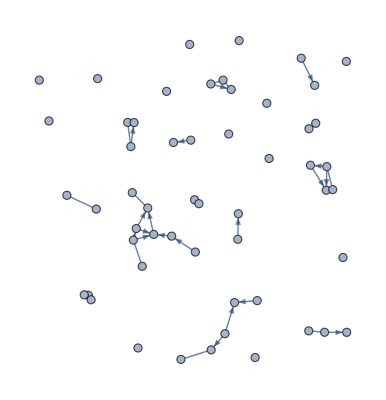

```mathematica
𝒢=RandomWeightedMixedGraph[SpatialGraphDistribution[54,0.1],0.68,RandomInteger[{1,7}]&]
```

Take the largest graph component by edge count:

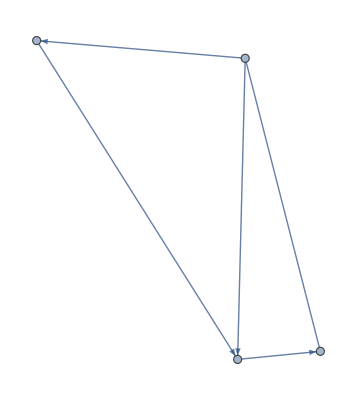

```mathematica
TakeLargestGraphComponentBy[𝒢,EdgeCount]
```

## Graphical Sequence

The degree sequence of a graph can be computed with VertexDegree. I created a function GraphicalDegreeSequenceQ that evaluates if a sequence is graphical. One condition for a sequence to be graphical is for the sum to be even.

```mathematica
randomSequence=RandomInteger[{1,7},7]
```

{4,4,2,3,5,4,5}

Compute if this random sequence is a graphical sequence;

```mathematica
GraphicalDegreeSequenceQ[randomSequence]
```

False

The total is not even:

```mathematica
EvenQ[Total[randomSequence]]
```

False

Evenness is a necessary but not a sufficient condition. A sequence can have an even sum and not be graphical.

I created two functions that function like RandomMixedGraph and RandomWeightedMixedGraph that assign names to the nodes:

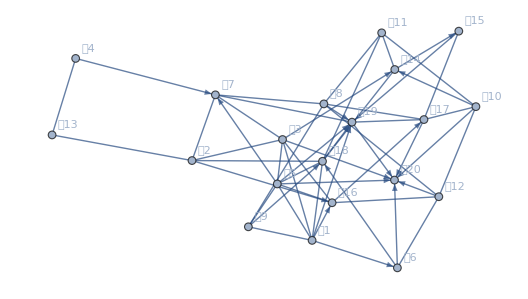

```mathematica
RandomSymbolicMixedGraph[{20,54},0.68,𝓊,VertexLabels->Automatic]
```

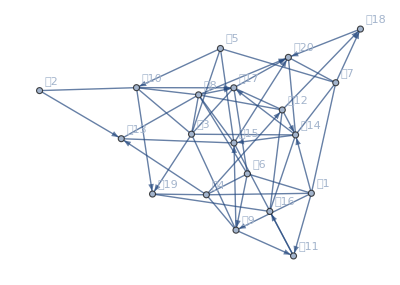

```mathematica
RandomSymbolicWeightedMixedGraph[{20,54},0.68,RandomInteger[{1,7}]&,𝓋,VertexLabels->Automatic]
```

I created a function to compute the convex hull of a graph based on a starting subset of the nodes:

Create a graph:

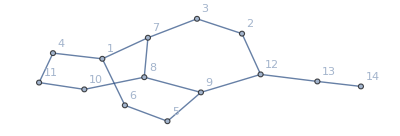

```mathematica
example=Graph[{1<->4,4<->11,11<->10,10<->8,8<->7,7<->1,8<->9,7<->3,2<->3,2<->12,12<->13,13<->14,12<->9,9<->5,5<->6,6<->1},VertexLabels->Automatic]
```

Find the convex hull starting with nodes 1, 2, and 9:

```mathematica
GraphConvexHull[example,{1,2,9}]
```

{1,2,3,5,6,7,8,9,12}

## Eulerizing Graphs

I created a function that Eulerizes unweighted undirected graphs and weighted undirected graphs.

Create a random graph

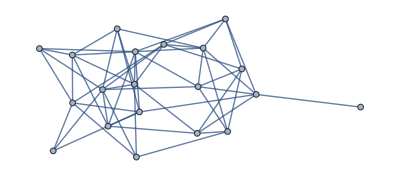

```mathematica
𝒢=RandomGraph[{20,54}]
```

Take the largest connected component to ensure that the graph is connected

```mathematica
TakeLargestGraphComponentBy[𝒢]
```

{-Graphics-}

```mathematica
𝒢=First[TakeLargestGraphComponentBy[𝒢]]
```

-Graphics-

𝒢 is not Eulerian

```mathematica
EulerianGraphQ[𝒢]
```

False

Make the graph 𝒢 Eulerian:

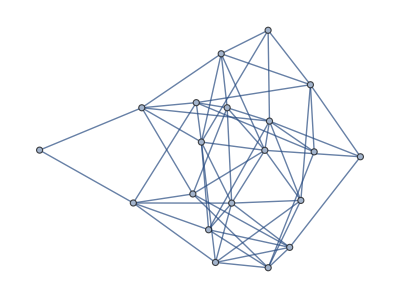

```mathematica
EulerizeGraph[𝒢]
```

The output is now Eulerian

```mathematica
EulerianGraphQ[EulerizeGraph[𝒢]]
```

True

Eulerize a weighted undirected cost by minimizing the sum of added costs:

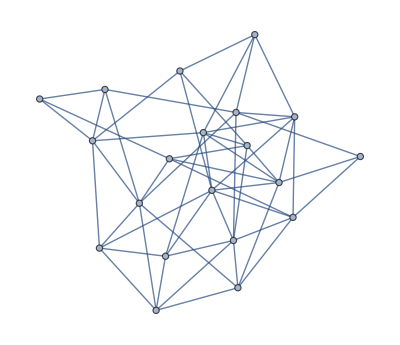

```mathematica
randomGraph=RandomWeightedMixedGraph[{20,54},0,RandomReal[]&]
```

Eulerize the random weighted undirected graph:

```mathematica
EulerizeGraph[randomGraph]
```

-Graphics-

Find the total cost of all the edges:

```mathematica
Total[AnnotationValue[EulerizeGraph[randomGraph],EdgeWeight]]
```

27.7021

Verify the output is an Eulerian graph:

```mathematica
EulerianGraphQ[EulerizeGraph[RandomWeightedMixedGraph[{20,54},0,RandomReal[]&]]]
```

True

I can solve the mixed Chinese Postman Problem by Eulerizing a mixed graph. However, I have not fully figured this out yet.

My functions are built into a paclet named Mixed Graphs that can be loaded from the Paclet Repository. I will continue to update the paclet.